```mathematica
f[x_, y_] := 2x+y^2;
x0=0; y0=0.3; xMax=1;
```

```mathematica
Euler[f_, x0_, y0_, h_, xMax_]:=Module[
{pts={{x0, y0}}, x=x0, y=y0, k1, yPred},
While[x<xMax - 10^-12,
k1=f[x, y];
yPred=y+h k1;
y=y+(h/2)(k1+f[x+h, yPred]);
x=x+h;
AppendTo[pts, {x, y}];
];
pts];
```

```mathematica
Rung[f_, x0_, y0_, h_, xMax_] := Module[
{pts={{x0, y0}}, x=x0, y=y0, k1, k2, k3, k4},
While[x<xMax - 10^-12,
k1=f[x, y];
k2=f[x+h/2, y+h k1/2];
k3=f[x+h/2, y+h k2/2];
k4=f[x+h/2, y+h k3];
y=y+(h/6)(k1+2 k2+2 k3+k4 );
x = x+h;
AppendTo[pts, {x, y}];
];pts];
```

```mathematica
exact =DSolve[{y'[x]==f[x, y[x]], y[0]==y0}, y, x];
exactNum =NDSolveValue[{y'[x]==f[x, y[x]], y[0]==y0}, y, {x, x0, xMax}];
```

```mathematica
ec1=Euler[f, x0, y0, 0.1,xMax];
ec2=Euler[f, x0, y0, 0.05,xMax];
r1=Rung[f, x0, y0, 0.1,xMax];
r2=Rung[f, x0, y0, 0.05,xMax];
```

```mathematica
Err[pts_, sol_] := N[Mean[Abs[pts[[All, 2]]-sol /@ pts[[All, 1]]]]];
```

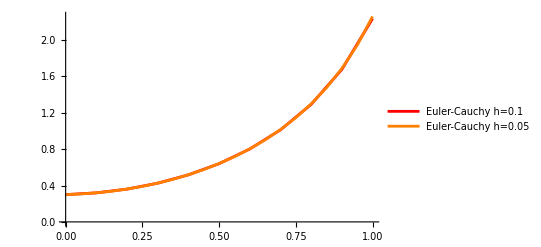

Error Euler-Cauchy h=0.1: 0.00605244

Error Euler-Cauchy h=0.05: 0.00139065

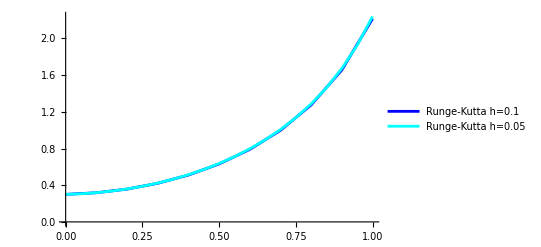

Error Runge-Kutta h=0.1: 0.0153095

Error Runge-Kutta h=0.05: 0.00757142

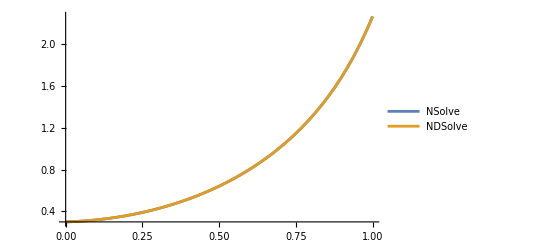

```mathematica
ListLinePlot[{ec1, ec2}, PlotStyle->{Red, Orange}, PlotLegends->{"Euler-Cauchy h=0.1", "Euler-Cauchy h=0.05"}]
Print["Error Euler-Cauchy h=0.1: ", Err[ec1, exactNum]];
Print["Error Euler-Cauchy h=0.05: ", Err[ec2, exactNum]];
ListLinePlot[{r1, r2}, PlotStyle->{Blue, Cyan}, PlotLegends->{"Runge-Kutta h=0.1", "Runge-Kutta h=0.05"}]
Print["Error Runge-Kutta h=0.1: ", Err[r1, exactNum]];
Print["Error Runge-Kutta h=0.05: ", Err[r2, exactNum]];

Plot[{y[x] /. exact[[1]], exactNum[x]}, {x, 0, 1},
PlotLegends->{"NSolve", "NDSolve"}]
```